## Forcing the frequencies

```mathematica
eq1:=X[r]+2G[r]-2A[r]==Subscript[γ, 1][r];
eq2:=X'[r]-2A'[r]-2G[r]A[r]+2G[r]X[r]-2 G[r]^2==(Subscript[ω, 1][r])^2;
eq3:=A[r]+X[r]-G[r]==Subscript[γ, 2][r];
eq4:=X'[r]-2G'[r]+G[r]X[r]-G[r]A[r]-2 G[r]^2-A[r]^2+A[r]X[r]==(Subscript[ω, 2][r])^2;
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
FullSimplify[eq4]
```

2 A[r]+γ_1[r]==2 G[r]+X[r]

2 G[r] (A[r]+G[r]-X[r])+ω_1[r]^2+2 A'[r]==X'[r]

A[r]+X[r]==G[r]+γ_2[r]

A[r]^2+A[r] G[r]+2 G[r]^2+ω_2[r]^2+2 G'[r]==(A[r]+G[r]) X[r]+X'[r]

```mathematica
Solve[eq1,X[r]]
```

{{X[r]→2 A[r]-2 G[r]+γ_1[r]}}

```mathematica
X[r_]:=2 A[r]-2 G[r]+Subscript[γ, 1][r];
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
FullSimplify[eq4]
```

True

2 G[r] (A[r]+γ_1[r])+γ_1'[r]==6 G[r]^2+ω_1[r]^2+2 G'[r]

3 A[r]+γ_1[r]==3 G[r]+γ_2[r]

A[r]^2+(A[r]+G[r]) γ_1[r]+2 A'[r]+γ_1'[r]==G[r] (A[r]+4 G[r])+ω_2[r]^2+4 G'[r]

```mathematica
Solve[eq3,A[r]]
```

{{A[r]→1/3 (3 G[r]-γ_1[r]+γ_2[r])}}

```mathematica
A[r_]:=1/3 (3 G[r]-Subscript[γ, 1][r]+Subscript[γ, 2][r]);
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
FullSimplify[eq4]
```

True

2/3 G[r] (2 γ_1[r]+γ_2[r])+γ_1'[r]==4 G[r]^2+ω_1[r]^2+2 G'[r]

True

36 G[r]^2+2 γ_1[r]^2+9 (ω_2[r]^2+2 G'[r])==γ_1[r] γ_2[r]+γ_2[r]^2+3 G[r] (5 γ_1[r]+γ_2[r])+3 γ_1'[r]+6 γ_2'[r]

```mathematica
FullSimplify[Solve[eq2,G'[r]]]
```

{{G'[r]→1/6 (2 G[r] (-6 G[r]+2 γ_1[r]+γ_2[r])-3 ω_1[r]^2+3 γ_1'[r])}}

```mathematica
G'[r_]:=1/6 (2 G[r] (-6 G[r]+2 Subscript[γ, 1][r]+Subscript[γ, 2][r])-3 (Subscript[ω, 1][r])^2+3 Subscript[γ, 1]'[r]);
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
FullSimplify[eq4]
```

True

True

True

(3 G[r]-2 γ_1[r]-γ_2[r]) (γ_1[r]-γ_2[r])+9 ω_1[r]^2+6 γ_2'[r]==9 ω_2[r]^2+6 γ_1'[r]

```mathematica
FullSimplify[Solve[eq4,G[r]]]
```

{{G[r]→((γ_1[r]-γ_2[r]) (2 γ_1[r]+γ_2[r])-9 ω_1[r]^2+9 ω_2[r]^2+6 γ_1'[r]-6 γ_2'[r])/(3 (γ_1[r]-γ_2[r]))}}

```mathematica
G[r_]:=((Subscript[γ, 1][r]-Subscript[γ, 2][r]) (2 Subscript[γ, 1][r]+Subscript[γ, 2][r])-9 (Subscript[ω, 1][r])^2+9 (Subscript[ω, 2][r])^2+6 Subscript[γ, 1]'[r]-6 Subscript[γ, 2]'[r])/(3 (Subscript[γ, 1][r]-Subscript[γ, 2][r]));
FullSimplify[eq1]
FullSimplify[eq2]
FullSimplify[eq3]
FullSimplify[eq4]
FullSimplify[A[r]]
FullSimplify[G[r]]
FullSimplify[X[r]]
```

True

1/(γ_1[r]-γ_2[r])(8 γ_1[r]^4-8 γ_1[r]^3 γ_2[r]+2 γ_2[r]^4+54 (2 ω_1[r]^2-2 ω_2[r]^2-γ_1'[r]+γ_2'[r]) (3 ω_1[r]^2-3 ω_2[r]^2-2 γ_1'[r]+2 γ_2'[r])-3 γ_1[r]^2 (2 γ_2[r]^2+33 ω_1[r]^2-36 ω_2[r]^2-25 γ_1'[r]+22 γ_2'[r])+γ_2[r]^2 (63 ω_1[r]^2-54 ω_2[r]^2-33 γ_1'[r]+42 γ_2'[r])+36 γ_2[r] (3 ω_1[r] ω_1'[r]-3 ω_2[r] ω_2'[r]-γ_1''[r]+γ_2''[r])+2 γ_1[r] (2 γ_2[r]^3+3 γ_2[r] (6 ω_1[r]^2-9 ω_2[r]^2-7 γ_1'[r]+4 γ_2'[r])-18 (3 ω_1[r] ω_1'[r]-3 ω_2[r] ω_2'[r]-γ_1''[r]+γ_2''[r])))==0

True

1/(γ_1[r]-γ_2[r])(8 γ_1[r]^4-8 γ_1[r]^3 γ_2[r]+2 γ_2[r]^4+54 (2 ω_1[r]^2-2 ω_2[r]^2-γ_1'[r]+γ_2'[r]) (3 ω_1[r]^2-3 ω_2[r]^2-2 γ_1'[r]+2 γ_2'[r])-3 γ_1[r]^2 (2 γ_2[r]^2+33 ω_1[r]^2-36 ω_2[r]^2-25 γ_1'[r]+22 γ_2'[r])+γ_2[r]^2 (63 ω_1[r]^2-54 ω_2[r]^2-33 γ_1'[r]+42 γ_2'[r])+36 γ_2[r] (3 ω_1[r] ω_1'[r]-3 ω_2[r] ω_2'[r]-γ_1''[r]+γ_2''[r])+2 γ_1[r] (2 γ_2[r]^3+3 γ_2[r] (6 ω_1[r]^2-9 ω_2[r]^2-7 γ_1'[r]+4 γ_2'[r])-18 (3 ω_1[r] ω_1'[r]-3 ω_2[r] ω_2'[r]-γ_1''[r]+γ_2''[r])))==0

(γ_1[r]^2+γ_1[r] γ_2[r]-2 γ_2[r]^2-9 ω_1[r]^2+9 ω_2[r]^2+6 γ_1'[r]-6 γ_2'[r])/(3 γ_1[r]-3 γ_2[r])

((γ_1[r]-γ_2[r]) (2 γ_1[r]+γ_2[r])-9 ω_1[r]^2+9 ω_2[r]^2+6 γ_1'[r]-6 γ_2'[r])/(3 (γ_1[r]-γ_2[r]))

1/3 (γ_1[r]+2 γ_2[r])

```mathematica
HC1:=B''[r]+B[r]*(X'[r]-2*A'[r])+B'[r]*(-2*A[r]+X[r]+2*G[r])-2*G[r]*B[r]*(A[r]-X[r]+G[r]);
HC2:=F''[r]+F[r]*(X'[r]-2*G'[r])+F'[r]*(A[r]+X[r]-G[r])+F[r]*(G[r]*(X[r]-A[r]-2G[r])-A[r]*(A[r]-X[r]))-G[r];
FullSimplify[HC1==0]
FullSimplify[DSolve[HC1==0,B[r],r]]
FullSimplify[HC2==0]
FullSimplify[DSolve[HC2==0,F[r],r]]
```

2 B[r] (2 γ_1+γ_2)^2==9 (γ_1 B'[r]+B''[r])

{{B[r]→ⅇ^(-1/6 r (3 γ_1+√(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2))) (C[1]+ⅇ^(1/3 r √(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2)) C[2])}}

(2 γ_1+γ_2) (3+2 F[r] (2 γ_1+γ_2))==9 (γ_2 F'[r]+F''[r])

{{F[r]→ⅇ^(-1/6 r (3 γ_2+√(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2))) (C[1]+ⅇ^(1/3 r √(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2)) C[2])-3/(4 γ_1+2 γ_2)}}

```mathematica
B[r_]:=ⅇ^(-1/6 r (3 Subscript[γ, 1]+√(41 Subscript[γ, 1]^2+32 Subscript[γ, 1] Subscript[γ, 2]+8 Subscript[γ, 2]^2))) (C[1]+ⅇ^(1/3 r √(41 Subscript[γ, 1]^2+32 Subscript[γ, 1] Subscript[γ, 2]+8 Subscript[γ, 2]^2)) C[2]);
F[r_]:=ⅇ^(-1/6 r (3 Subscript[γ, 2]+√(32 Subscript[γ, 1]^2+32 Subscript[γ, 1] Subscript[γ, 2]+17 Subscript[γ, 2]^2))) (C[3]+ⅇ^(1/3 r √(32 Subscript[γ, 1]^2+32 Subscript[γ, 1] Subscript[γ, 2]+17 Subscript[γ, 2]^2)) C[4])-3/(4 Subscript[γ, 1]+2 Subscript[γ, 2]);
```

```mathematica
Rtt[r_]:=B'[r]+B[r]*(2*G[r]+X[r]-A[r]);
Rrr[r_]:=A'[r]+2G'[r]+A[r]A[r]+2G[r]G[r]-A[r]X[r]-2X[r]G[r];
Rthth[r_]:=F'[r]+F[r](A[r]+X[r])+1;
FullSimplify[Rtt[r]]
FullSimplify[Rrr[r]]
FullSimplify[Rthth[r]]
```

1/6 ⅇ^(-1/6 r (3 γ_1+√(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2))) (C[1] (5 γ_1+4 γ_2)+ⅇ^(1/3 r √(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2)) C[2] (5 γ_1+4 γ_2)-C[1] √(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2)+ⅇ^(1/3 r √(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2)) C[2] √(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2))

2/9 (γ_1-γ_2) (2 γ_1+γ_2)

1/6 (-6+(18 γ_1)/(2 γ_1+γ_2)+ⅇ^(-1/6 r (3 γ_2+√(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2))) (C[3]+ⅇ^(1/3 r √(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2)) C[4]) (4 γ_1+5 γ_2)-ⅇ^(-1/6 r (3 γ_2+√(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2))) C[3] √(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2)+ⅇ^(1/6 r (-3 γ_2+√(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2))) C[4] √(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2))

## Auto-parallel curves

```mathematica
eq1t[τ_]:=t''[τ]+2*A[r[τ]]*r'[τ]*t'[τ];
FullSimplify[eq1t[τ]]
eq1r[τ_]=r''[τ]+B[r[τ]]*t'[τ]^2+X[r[τ]]*r'[τ]^2+F[r[τ]]*θ'[τ]^2+F[r[τ]]*ϕ'[τ]^2*Sin[θ]^2;
FullSimplify[eq1r[τ]]
eq1th[τ_]=θ''[τ]+2*G[r[τ]]*θ'[τ]*r'[τ]-Cos[θ]*Sin[θ]*ϕ'[τ]^2;
FullSimplify[eq1th[τ]]
eq1ph[τ_]=ϕ''[τ]+2*G[r[τ]]*ϕ'[τ]*r'[τ]+Cos[θ]/Sin[θ]*ϕ'[τ]*θ'[τ];
FullSimplify[eq1ph[τ]]
```

2/3 (γ_1+2 γ_2) r'[τ] t'[τ]+t''[τ]

1/3 (γ_1+2 γ_2) r'[τ]^2+ⅇ^(-1/6 r[τ] (3 γ_1+√(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2))) (C[1]+ⅇ^(1/3 r[τ] √(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2)) C[2]) t'[τ]^2+1/2 (2 ⅇ^(-1/6 r[τ] (3 γ_2+√(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2))) (C[3]+ⅇ^(1/3 r[τ] √(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2)) C[4])-3/(2 γ_1+γ_2)) (θ'[τ]^2+Sin[θ]^2 ϕ'[τ]^2)+r''[τ]

2/3 (2 γ_1+γ_2) r'[τ] θ'[τ]-Cos[θ] Sin[θ] ϕ'[τ]^2+θ''[τ]

2/3 (2 γ_1+γ_2) r'[τ] ϕ'[τ]+Cot[θ] θ'[τ] ϕ'[τ]+ϕ''[τ]

Fixing θ=π/2

```mathematica
eq1t[τ_]:=t''[τ]+2*A[r[τ]]*r'[τ]*t'[τ];
FullSimplify[eq1t[τ]]
eq1r[τ_]=r''[τ]+B[r[τ]]*t'[τ]^2+X[r[τ]]*r'[τ]^2+F[r[τ]]*ϕ'[τ]^2;
FullSimplify[eq1r[τ]]
eq1ph[τ_]=ϕ''[τ]+2*G[r[τ]]*ϕ'[τ]*r'[τ];
FullSimplify[eq1ph[τ]]
```

2/3 (γ_1+2 γ_2) r'[τ] t'[τ]+t''[τ]

1/3 (γ_1+2 γ_2) r'[τ]^2+ⅇ^(-1/6 r[τ] (3 γ_1+√(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2))) (C[1]+ⅇ^(1/3 r[τ] √(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2)) C[2]) t'[τ]^2+(ⅇ^(-1/6 r[τ] (3 γ_2+√(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2))) (C[3]+ⅇ^(1/3 r[τ] √(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2)) C[4])-3/(4 γ_1+2 γ_2)) ϕ'[τ]^2+r''[τ]

2/3 (2 γ_1+γ_2) r'[τ] ϕ'[τ]+ϕ''[τ]

```mathematica
DSolve[2/3 (2 Subscript[γ, 1]+Subscript[γ, 2]) r'[τ] ϕ'[τ]+ϕ''[τ]==0,ϕ[τ],τ]
```

{{ϕ[τ]→C[2]+ⅇ^(-4/3 r[K[1]] γ_1-2/3 r[K[1]] γ_2) C[1]K[1]1τ}}

```mathematica
D[C[2]+ⅇ^(-4/3 r[K[1]] Subscript[γ, 1]-2/3 r[K[1]] Subscript[γ, 2]) C[1]K[1]1τ,τ]
```

ⅇ^(-4/3 r[τ] γ_1-2/3 r[τ] γ_2) C[1]

```mathematica
ϕ[τ_]:=C[2]+ⅇ^(-4/3 r[K[1]] Subscript[γ, 1]-2/3 r[K[1]] Subscript[γ, 2]) C[1]K[1]1τ;
eq1t[τ_]:=t''[τ]+2*A[r[τ]]*r'[τ]*t'[τ];
FullSimplify[eq1t[τ]]
eq1r[τ_]=r''[τ]+B[r[τ]]*t'[τ]^2+X[r[τ]]*r'[τ]^2+F[r[τ]]*ϕ'[τ]^2;
FullSimplify[eq1r[τ]]
eq1ph[τ_]=ϕ''[τ]+2*G[r[τ]]*ϕ'[τ]*r'[τ];
FullSimplify[eq1ph[τ]]
```

2/3 (γ_1+2 γ_2) r'[τ] t'[τ]+t''[τ]

ⅇ^(-4/3 r[τ] (2 γ_1+γ_2)) C[1]^2 (ⅇ^(-1/6 r[τ] (3 γ_2+√(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2))) (C[3]+ⅇ^(1/3 r[τ] √(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2)) C[4])-3/(4 γ_1+2 γ_2))+1/3 (γ_1+2 γ_2) r'[τ]^2+ⅇ^(-1/6 r[τ] (3 γ_1+√(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2))) (C[1]+ⅇ^(1/3 r[τ] √(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2)) C[2]) t'[τ]^2+r''[τ]

0

```mathematica
DSolve[2/3 (Subscript[γ, 1]+2 Subscript[γ, 2]) r'[τ] t'[τ]+t''[τ]==0,t[τ],τ]
```

{{t[τ]→C[2]+ⅇ^(-2/3 r[K[1]] γ_1-4/3 r[K[1]] γ_2) C[1]K[1]1τ}}

```mathematica
D[C[2]+ⅇ^(-2/3 r[K[1]] Subscript[γ, 1]-4/3 r[K[1]] Subscript[γ, 2]) C[1]K[1]1τ,τ]
```

ⅇ^(-2/3 r[τ] γ_1-4/3 r[τ] γ_2) C[1]

```mathematica
t[τ_]:=C[2]+ⅇ^(-2/3 r[K[1]] Subscript[γ, 1]-4/3 r[K[1]] Subscript[γ, 2]) C[1]K[1]1τ;
eq1t[τ_]:=t''[τ]+2*A[r[τ]]*r'[τ]*t'[τ];
FullSimplify[eq1t[τ]]
eq1r[τ_]=r''[τ]+B[r[τ]]*t'[τ]^2+X[r[τ]]*r'[τ]^2+F[r[τ]]*ϕ'[τ]^2;
FullSimplify[eq1r[τ]]
eq1ph[τ_]=ϕ''[τ]+2*G[r[τ]]*ϕ'[τ]*r'[τ];
FullSimplify[eq1ph[τ]]
```

0

ⅇ^(-1/6 r[τ] (11 γ_1+16 γ_2+√(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2))) C[1]^2 (C[1]+ⅇ^(1/3 r[τ] √(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2)) C[2])+ⅇ^(-4/3 r[τ] (2 γ_1+γ_2)) C[1]^2 (ⅇ^(-1/6 r[τ] (3 γ_2+√(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2))) (C[3]+ⅇ^(1/3 r[τ] √(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2)) C[4])-3/(4 γ_1+2 γ_2))+1/3 (γ_1+2 γ_2) r'[τ]^2+r''[τ]

0

```mathematica
Reduce[41 Subscript[γ, 1]^2+32 Subscript[γ, 1] Subscript[γ, 2]+8 Subscript[γ, 2]^2>0,Subscript[γ, 1]]
```

γ_1∈ℝ&&(γ_2<0||(γ_2==0&&(γ_1<0||γ_1>0))||γ_2>0)

```mathematica
Reduce[41 Subscript[γ, 1]^2+32 Subscript[γ, 1] Subscript[γ, 2]+8 Subscript[γ, 2]^2>0,Subscript[γ, 2]]
```

γ_2∈ℝ&&(γ_1<0||(γ_1==0&&(γ_2<0||γ_2>0))||γ_1>0)

## Case I

For this configuration, the c1 constant makes the width of the solution bigger for small values regardless if it is positive or negative.

3/2 ⅇ^((4 r[τ])/3)+2 ⅇ^((37 r[τ])/6) Cosh[1/6 √17 r[τ]]+2 ⅇ^((17 r[τ])/6) Cosh[1/6 √89 r[τ]]-5/3 r'[τ]^2+r''[τ]

{{r[τ]→InterpolatingFunction[…][τ]}}

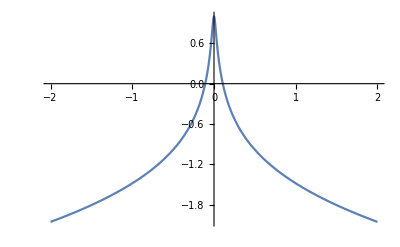

```mathematica
Subscript[γ, 1]=1;Subscript[γ, 2]=-3;
eq1r[τ_]=r''[τ]+B[r[τ]]*t'[τ]^2+X[r[τ]]*r'[τ]^2+F[r[τ]]*ϕ'[τ]^2;
FullSimplify[eq1r[τ]/.{C[1]->1,C[2]->1,C[3]->1,C[4]->1}]
s=NDSolve[{%==0,r[0]==1,r'[0]==0},r[τ],{τ,-2,2}]
Plot[r[τ]/.s,{τ,-2,2}]
```

```mathematica
FullSimplify[Rtt[r]]
FullSimplify[Rrr[r]]
FullSimplify[Rthth[r]]
```

1/6 ⅇ^(-1/6 (3+√17) r) (-((7+√17) C[1])+(-7+√17) ⅇ^((√17 r)/3) C[2])

-8/9

-4+1/6 ⅇ^(-1/6 (-9+√89) r) (-((11+√89) C[3])+(-11+√89) ⅇ^((√89 r)/3) C[4])

## Case II

0.01 ⅇ^(0.000133332 r[τ])+150. ⅇ^(0.000133333 r[τ])+0.01 ⅇ^(2.00023 r[τ])-0.001 ⅇ^(3.00027 r[τ])-0.001 ⅇ^(4.00027 r[τ])-1.00007 r'[τ]^2+r''[τ]

{{r[τ]→InterpolatingFunction[…][τ]}}

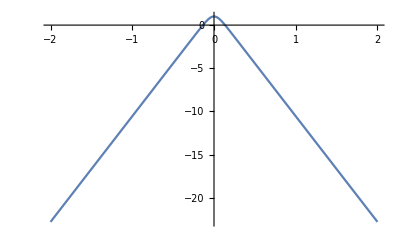

```mathematica
Subscript[γ, 1]=1;Subscript[γ, 2]=-2.0001;
eq1r[τ_]=r''[τ]+B[r[τ]]*t'[τ]^2+X[r[τ]]*r'[τ]^2+F[r[τ]]*ϕ'[τ]^2;
FullSimplify[eq1r[τ]/.{C[1]->-0.1,C[2]->-0.1,C[3]->1,C[4]->1}]
s=NDSolve[{%==0,r[0]==1,r'[0]==0},r[τ],{τ,-2,2}]
Plot[r[τ]/.s,{τ,-2,2}]
```

```mathematica
FullSimplify[Rtt[r]]
FullSimplify[Rrr[r]]
FullSimplify[Rthth[r]]
```

1/6 ⅇ^(-1/6 (3+√17) r) (-((7+√17) C[1])+(-7+√17) ⅇ^((√17 r)/3) C[2])

-8/9

-4+1/6 ⅇ^(-1/6 (-9+√89) r) (-((11+√89) C[3])+(-11+√89) ⅇ^((√89 r)/3) C[4])

## AdS/dS

From the PAG model

```mathematica
Rtt[r_]:=B'[r]+B[r]*(2*G[r]+X[r]-A[r]);
Rrr[r_]:=A'[r]+2G'[r]+A[r]A[r]+2G[r]G[r]-A[r]X[r]-2X[r]G[r];
Rthth[r_]:=F'[r]+F[r](A[r]+X[r])+1;
FullSimplify[Rtt[r]]
FullSimplify[Rrr[r]]
FullSimplify[Rthth[r]]
```

1/6 ⅇ^(-1/6 r (3 γ_1+√(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2))) (C[1] (5 γ_1+4 γ_2)+ⅇ^(1/3 r √(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2)) C[2] (5 γ_1+4 γ_2)-C[1] √(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2)+ⅇ^(1/3 r √(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2)) C[2] √(41 γ_1^2+32 γ_1 γ_2+8 γ_2^2))

2/9 (γ_1-γ_2) (2 γ_1+γ_2)

1/6 (-6+(18 γ_1)/(2 γ_1+γ_2)+ⅇ^(-1/6 r (3 γ_2+√(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2))) (C[3]+ⅇ^(1/3 r √(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2)) C[4]) (4 γ_1+5 γ_2)-ⅇ^(-1/6 r (3 γ_2+√(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2))) C[3] √(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2)+ⅇ^(1/6 r (-3 γ_2+√(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2))) C[4] √(32 γ_1^2+32 γ_1 γ_2+17 γ_2^2))

```mathematica
Limit[Rtt[r],r->∞]
FullSimplify[Limit[Rrr[r],r->∞]]
Limit[Rthth[r],r->∞]
```

ConditionalExpression[∞, ]

2/9 (γ_1-γ_2) (2 γ_1+γ_2)

ConditionalExpression[∞, ]

De Sitter metric

```mathematica
gtt[r_]:=-(1-(2*a)/r-b*r^2);
grr[r_]:=1/(1-(2*a)/r-b*r^2) ;
gthth[r_]:=r^2;
Limit[gtt[r],r->∞]
FullSimplify[Limit[grr[r],r->∞]]
Limit[gthth[r],r->∞]
```

b ∞

0

∞

Anti de Sitter

```mathematica
gtt[r_]:=-(1-a/r+b*r^2);
grr[r_]:=1/(1-a/r+b*r^2) ;
gthth[r_]:=r^2;
gthth[r_]:=r^2;
Limit[gtt[r],r->∞]
FullSimplify[Limit[grr[r],r->∞]]
Limit[gthth[r],r->∞]
```

b (-∞)

0

∞